This script is a part of ANGEL project.
V 1.3
2017.10.01
(C) Vulpes Corsac

```mathematica
Clear["Global`*"];(* Variables clearing *)
```

```mathematica
(* FILE NAMES SHOULD BE e.g. "T=20,3.dat" || "T=20.dat" *)
```

```mathematica
paraboloid[y0_,A_,μ_,x_] := y0 + A(x-μ)^2;(* Paraboloid fitting function *)
linear[A_,B_,x_] := A x+B;(* Linear fitting function *)
```

```mathematica
phaseColumnName="Theta"; (* Name of column in data file with phase *)
frequencyColumnName="Fext";(* Name of column in data file with frequency *)
```

```mathematica
parabolicPart=2;(* Part of data (from Min to (Max-Min)/part) selection *)
```

```mathematica
fileNames = FileNames["T=*.dat",NotebookDirectory[]];(* Getting all file names that matches template in current directory *)
FresFromTemperature=Table[(* Getting resonance frequency from all temperature data *)
file = FileNameSplit[fileNames[[i]]][[-1]];(* Getting current filename *)
split=StringSplit[StringSplit[file,"."][[1]],"="][[-1]];(* Getting temperature *)
split1 = StringSplit[split,","];(* Splitting coma *)
Temperature = Which[(* If there is coma in file name *)
Length[split1]==1,ToExpression[split1[[1]]],(* No - Ok *)
Length[split1]==2,ToExpression[split1[[1]]<>"."<>split1[[2]]](* Yes - Merging temperature string and convert to floats *)
];
DataNames=Import[NotebookDirectory[]<>file][[1]];(* Getting data header *)
Data=Import[NotebookDirectory[]<>file][[2;;]];(* Getting current temperature data *)
RoundData = Transpose[
{Data[[All,Position[DataNames,frequencyColumnName][[1,1]]]],
Data[[All,Position[DataNames,phaseColumnName][[1,1]]]]}
];(* Cutting away all unnesessary data *)
FresMin=RoundData[[Ordering[RoundData[[All, 2]],1], 1]][[1]];(* Getting resonance frequency by finding minimum *)
PhaseMin=Min[RoundData[[All,2]]];(* Getting phase minimum *)
PhaseMax=Max[RoundData[[All,2]]];(* Getting phase maximum *)
RoundDataParaboloid =Select[RoundData,PhaseMin≤#[[2]]≤PhaseMin+(PhaseMax-PhaseMin)/parabolicPart&] ;(* Cutting data only around phase minimum *)
nlmRoundParaboloid = NonlinearModelFit[(* Fitting data with paraboloid *)
RoundDataParaboloid,paraboloid[y0,A,μ,t],
{{y0,Max[RoundDataParaboloid[[All,2]]]},
{A,RoundDataParaboloid[[Ordering[RoundDataParaboloid[[All, 2]],1], 2]][[1]]},
{μ,RoundDataParaboloid[[Ordering[RoundDataParaboloid[[All, 2]],1], 1]][[1]]}},
t];
parametersTableRoundParaboloid = nlmRoundParaboloid["ParameterTable"];(* Getting fitted parameters *)
FresParaboloid = parametersTableRoundParaboloid[[1,1,4,2]];(* Getting resonance frequency from fitting *)
ΔFresParaboloid = 100×Abs[parametersTableRoundParaboloid[[1,1,4,3]]/parametersTableRoundParaboloid[[1,1,4,2]]];(* Getting resonance frequency deviation from fitting *)
Export[NotebookDirectory[]<>"T="<>StringReplace[ToString[Temperature],"."->","]<>".png",(* Exporting plot with data and fitting *)
Show[
ListPlot[RoundData,PlotRange->All, Joined->False,ImageSize->Large,Filling->None,
PlotLabel->"Phase fitting for T = "<>ToString[Temperature],AxesLabel->{"Frequency[Hz]","Phase[Deg]"}],
Plot[paraboloid[parametersTableRoundParaboloid [[1,1,2,2]],parametersTableRoundParaboloid [[1,1,3,2]],parametersTableRoundParaboloid [[1,1,4,2]],t],{t,RoundDataParaboloid[[1,1]],RoundDataParaboloid[[-1,1]]},PlotRange->All,ImageSize->Large,ColorFunction->Function[{x,y},Red]]
]
];
{Temperature,FresParaboloid,FresMin,ΔFresParaboloid},{i,1,Length[fileNames]}];
(FresFromTemperatureExport = Insert[FresFromTemperature,{"T[C]","FresFit[Hz]","FresMin[Hz]","dFresFit[%]"},1])//TableForm(* Showing everythin in a table *)
Export[NotebookDirectory[]<>"FresFromTemperature.xlsx",FresFromTemperatureExport];(* Exporting data from above *)
```

T[C] | FresFit[Hz] | FresMin[Hz] | dFresFit[%]
20.47 | 580417.56004060737589 | 580419. | 0.00006802987885565
22.5 | 580372.85366739425118 | 580370. | 0.00005104371008104
25.1 | 580295.38808930465416 | 580294. | 0.00005922559091183
28.4 | 580183.01140012393867 | 580187. | 0.000061088622123

```mathematica
KprtData=Transpose[{FresFromTemperature[[All,1]],FresFromTemperature[[All,2]]}];(* Forming data for later fitting *)
Which[(* Looking how many points we have *)
Length[FresFromTemperature[[All,1]]]==1,(* 1 point - nothing we can tell *)
Kprt=δKprt=F0=δF0=Infinity;
Length[FresFromTemperature[[All,1]]]==2,(* 2 points - no error *)
Kprt=(KprtData[[2,2]]-KprtData[[1,2]])/(KprtData[[2,1]]-KprtData[[1,1]]);δKprt=0;F0=KprtData[[1,2]];δF0=0;
Length[FresFromTemperature[[All,1]]]≥3,(* 3 or more points *)
KprtFit = NonlinearModelFit[KprtData,linear[A,B,x],{{A,1},{B,1}},x];(* Fitting *)
parametricTableKprtFit = KprtFit["ParameterTable"];(* Getting fitting parameters table, and coefficients and their errors *)
Kprt=parametricTableKprtFit[[1,1,2,2]];δKprt=Abs[parametricTableKprtFit[[1,1,2,3]]];
F0=parametricTableKprtFit[[1,1,3,2]];δF0=Abs[parametricTableKprtFit[[1,1,3,3]]];
];
```

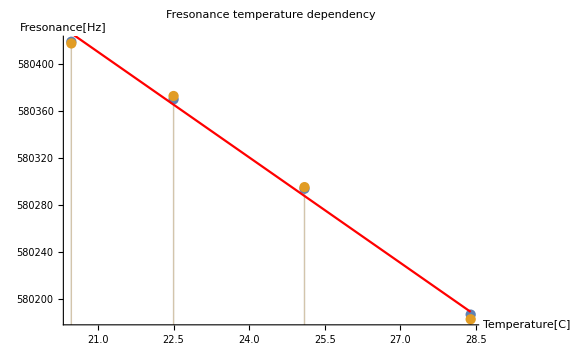

```mathematica
plotFresFromTemperature = 
Show[
ListPlot[Evaluate[{(* Plotting Min and Fit Fres *)
Transpose[{FresFromTemperature[[All,1]],FresFromTemperature[[All,3]]}],
Transpose[{FresFromTemperature[[All,1]],FresFromTemperature[[All,2]]}]
}],
PlotRange->All, Joined->False,ImageSize->Large,Filling->Axis,PlotLabel->"Fresonance temperature dependency",AxesLabel->{"Temperature[C]","Fresonance[Hz]"}],
Plot[F0+Kprt frequency,{frequency,Min[FresFromTemperature[[All,1]]],Max[FresFromTemperature[[All,1]]]},PlotRange->All,ImageSize->Large,ColorFunction->Function[{x,y},Red]]
]
Export[NotebookDirectory[]<>"FresFromTemperature.png",plotFresFromTemperature];(* Exporting plot from above *)
```

```mathematica
KprtString = (* Getting string with all parameters for later export *)
"Kprt[Hz/K] = "<>ToString[Kprt]<>" ± "<>ToString[δKprt]<>", t.m. "<> ToString[100×Abs[δKprt/Kprt]] <>" %"<>"\n"<>
"F0[kHz] = "<>ToString[0.001×F0]<>" ± "<>ToString[δF0]<>", t.m. "<> ToString[100×Abs[δF0/F0]] <>" %"<>"\n"<>
"F[Hz] = "<>ToString[Kprt]<>"*T[C] + 10^3*"<>ToString[0.001×F0]<>"\n"<>
"T[C] = "<>ToString[1/Kprt]<>"*F[Hz]+"<>ToString[-F0/Kprt]
Export[NotebookDirectory[]<>"Kprt.txt",KprtString];(* Exporting string from above *)
```

Kprt[Hz/K] = -29.8696 ± 1.78216, t.m. 5.96647 %
F0[kHz] = 581.038 ± 43.3054, t.m. 0.00745312 %
F[Hz] = -29.8696*T[C] + 10^3*581.038
T[C] = -0.0334789*F[Hz]+19452.5